```mathematica
MM[d_,ps_,η_]:=d(1-ps)+η ps;
NN[d_,ps_]:=1/((1-d)(1-ps))-1;
```

### β,γ=0

```mathematica
ρr1=({{α SuperStar[α]+δ (d-d p+p η)^2 SuperStar[δ], 0, 0, -((-1+d) (-1+p) α SuperStar[δ])/(-1+pr)}, {0, -(pr α η SuperStar[α]+δ (d (-1+p)-p η) (-1+p-p pr η^2+d (-1+p) (-1+pr η)) SuperStar[δ])/(-1+pr), 0, 0}, {0, 0, -(pr α η SuperStar[α]+δ (d (-1+p)-p η) (-1+p-p pr η^2+d (-1+p) (-1+pr η)) SuperStar[δ])/(-1+pr), 0}, {-((-1+d) (-1+p) δ SuperStar[α])/(-1+pr), 0, 0, (pr^2 α η^2 SuperStar[α]+δ (-1+p-p pr η^2+d (-1+p) (-1+pr η))^2 SuperStar[δ])/(-1+pr)^2}});
```

```mathematica
Max[0,1]
```

1

```mathematica
C2d[α_,δ_,d_]:=Max[
0,
2(1-d)(α δ-d δ^2)];
C2r[α_,δ_,d_,ps_,η_]:=Max[
0,2((α δ-MM[d,ps,η] δ^2-η N[d,ps](α^2+MM[d,ps,η]^2 δ^2))/((1+η NN[d,ps])^2 α^2+(1+MM[d,ps,η]+η MM[d,ps,η] N[d,ps])^2 δ^2))];
```

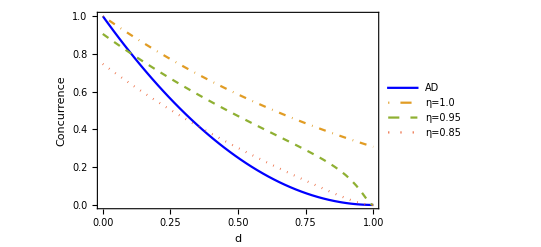

```mathematica
Plot[
{C2d[√(1/2),√(1/2),d],
C2r[√(1/2),√(1/2),d,0.5,0.0],
C2r[√(1/2),√(1/2),d,0.5,0.05],
C2r[√(1/2),√(1/2),d,0.5,0.15]
},
{d,0,1},
Frame->True,FrameLabel->{"d","Concurrence"},
FrameTicks->{{All,All},{All,All}},
RotateLabel->True,FrameStyle->Directive[Black],
PlotStyle->{Blue,DotDashed,Dashed,Dotted,},
PlotLegends->Placed[LineLegend[
{"AD","η=1.0","η=0.95","η=0.85"},LegendLayout->{"Row",2}],
{Right,Top}],
BaseStyle->{FontFamily->"Times", FontSize->12}]
```

```mathematica
?Frame
```

Frame is an option for Graphics, Grid, and other constructs that specifies whether to include a frame.

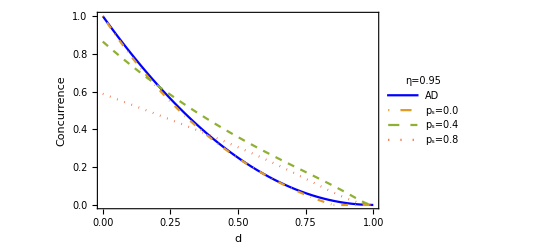

```mathematica
Plot[
{C2d[√(1/2),√(1/2),d],
C2r[√(1/2),√(1/2),d,0.0,0.1],
C2r[√(1/2),√(1/2),d,0.4,0.1],
C2r[√(1/2),√(1/2),d,0.8,0.1]
},
{d,0,1},
Frame->True,FrameLabel->{"d","Concurrence"},
FrameTicks->{{All,All},{All,All}},
RotateLabel->True,FrameStyle->Directive[Black],
BaseStyle->{FontFamily->"Times", FontSize->12},
PlotLegends->Placed[LineLegend[
{"AD","p_s=0.0","p_s=0.4","p_s=0.8"},
LegendLabel->"η=0.95",LegendLayout->{"Row",2}],
{Right,Top}],
PlotStyle->{Blue,DotDashed,Dashed,Dotted}]
```

```mathematica
Plot3D[
{C2r[√(1/2),√(1/2),0.2,ps,η]-C2d[√(1/2),√(1/2),0.2]},
{ps,0,1},{η,0,0.3},
AxesLabel->{"d","η"},
PlotRange->All]
```

-Graphics3D-

### α,δ=0

```mathematica
ρr2=({{-(-1+d)^2 (-1+p)^2 (d (-1+p)-p η) (β SuperStar[β]+γ SuperStar[γ]), 0, 0, 0}, {0, (-1+d) (-1+p) (β (1+d^2 (-1+p)^2 η+p (-1+p η^2)-d (-1+p) (-1+p η (1+η))) SuperStar[β]+(d (-1+p)-p) γ η (d (-1+p)-p η) SuperStar[γ]), (-1+d)^2 (-1+p)^2 β SuperStar[γ], 0}, {0, (-1+d)^2 (-1+p)^2 γ SuperStar[β], (-1+d) (-1+p) (γ SuperStar[γ]+(d (-1+p)-p) (γ SuperStar[γ]-η (d-d p+p η) (β SuperStar[β]+γ SuperStar[γ]))), 0}, {0, 0, 0, -(d (-1+p)-p) η (1+d^2 (-1+p)^2 η+p (-1+p η^2)-d (-1+p) (-1+p η (1+η))) (β SuperStar[β]+γ SuperStar[γ])}});
```

```mathematica
Tr[ρr2]//FullSimplify
```

-(-1+p+d (-1+p) (-1+η)-p η) (1+d^2 (-1+p)^2 (-1+η)+p (-1+η) (1+p η)-d (-1+p) p (-1+η^2)) (β β^*+γ γ^*)

```mathematica
C1d[β_,γ_,d_]:=2(1-d)β γ;
C1r[β_,γ_,d_,ps_,η_]:=Max[0,2(β γ-√(η MM[d,ps,η]N[d,ps](1+η MM[d,ps,η]N[d,ps])))/(MM[d,ps,η]+(1+η N[d,ps])(1+η MM[d,ps,η]N[d,ps]))];
```

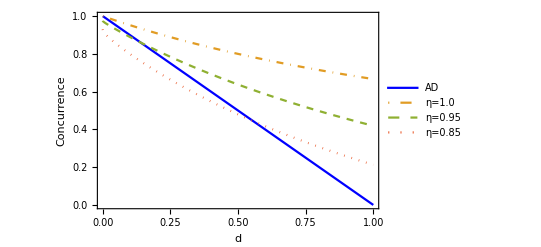

```mathematica
Plot[
{C1d[√(1/2),√(1/2),d],
C1r[√(1/2),√(1/2),d,0.5,0],
C1r[√(1/2),√(1/2),d,0.5,0.05],
C1r[√(1/2),√(1/2),d,0.5,0.15]
},
{d,0,1},
Frame->True,FrameLabel->{"d","Concurrence"},
FrameTicks->{{All,All},{All,All}},
RotateLabel->True,FrameStyle->Directive[Black],
PlotStyle->{Blue,DotDashed,Dashed,Dotted},
PlotLegends->Placed[LineLegend[{"AD","η=1.0","η=0.95","η=0.85"},
LegendLayout->{"Row",2}],
{Left,Bottom}],
BaseStyle->{FontFamily->"Times", FontSize->12},
PlotRange->{0.0,1.0}]
```

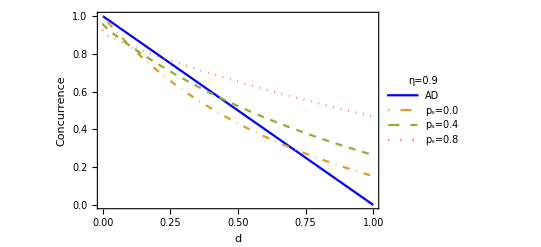

```mathematica
Plot[
{C1d[√(1/2),√(1/2),d],
C1r[√(1/2),√(1/2),d,0,0.1],
C1r[√(1/2),√(1/2),d,0.4,0.1],
C1r[√(1/2),√(1/2),d,0.8,0.1]
},
{d,0,1},
Frame->True,FrameLabel->{"d","Concurrence"},
FrameTicks->{{All,All},{All,All}},
RotateLabel->True,FrameStyle->Directive[Black],
PlotStyle->{Blue,DotDashed,Dashed,Dotted},
PlotLegends->Placed[LineLegend[
{"AD","p_s=0.0","p_s=0.4","p_s=0.8"},
LegendLabel->"η=0.9",
LegendLayout->{"Row",2}],{Left,Bottom}],
BaseStyle->{FontFamily->"Times", FontSize->12},
PlotRange->{0.0,1.0}]
```